```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Needs["VariationalMethods`"]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 366 Kb

{Utilities`CleanSlate`,TriangleLink`,CompiledFunctionTools`,IPOPTLink`,VariationalMethods`,DocumentationSearch`,ResourceLocator`,System`,Global`,Graphics`Mesh`,Graphics`PolygonUtils`}

```mathematica
J == ℐ θ'[t] + m r[t]^2 θ'[t]
```

J==ℐ θ'[t]+m r[t]^2 θ'[t]

```mathematica
Flatten[Solve[ J == ℐ θ'[t] + m r[t]^2 θ'[t]  , θ'[t]] ]
```

{θ'[t]→J/(ℐ+m r[t]^2)}

```mathematica
Clear[θtReplace]
θtReplace = 
Flatten[Solve[ J == ℐ θ'[t] + m r[t]^2 θ'[t]  , θ'[t]] ]
```

{θ'[t]→J/(ℐ+m r[t]^2)}

```mathematica
Clear[𝓇]
𝓇 = { r[t] Cos[θ[t]] , r[t] Sin[θ[t]] }
```

{Cos[θ[t]] r[t],r[t] Sin[θ[t]]}

```mathematica
D[𝓇, t]
```

{Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t],Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t]}

```mathematica
D[𝓇, t] . D[𝓇, t]
```

(Sin[θ[t]] r'[t]+Cos[θ[t]] r[t] θ'[t])^2+(Cos[θ[t]] r'[t]-r[t] Sin[θ[t]] θ'[t])^2

```mathematica
D[𝓇, t] . D[𝓇, t]  // Expand
```

Cos[θ[t]]^2 r'[t]^2+Sin[θ[t]]^2 r'[t]^2+Cos[θ[t]]^2 r[t]^2 θ'[t]^2+r[t]^2 Sin[θ[t]]^2 θ'[t]^2

```mathematica
D[𝓇, t] . D[𝓇, t]  // Expand  // Simplify
```

r'[t]^2+r[t]^2 θ'[t]^2

```mathematica
Clear[T]
T = 1/2 ℐ θ'[t]^2 + 1/2 m ( D[𝓇, t] . D[𝓇, t]  // Expand  // Simplify  )
```

1/2 ℐ θ'[t]^2+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

```mathematica
Clear[V]
V = 1/2 k ( r[t]-l )^2
```

1/2 k (-l+r[t])^2

```mathematica
T /. θtReplace  // Expand // Simplify
```

1/2 (J^2/(ℐ+m r[t]^2)+m r'[t]^2)

```mathematica
( T /. θtReplace  // Expand // Simplify  ) + V  // pdConv
```

1/2 (J^2/(m (r(t))^2+ℐ)+m ((∂r(t))/(∂t))^2)+1/2 k (r(t)-l)^2

```mathematica
Clear[ℒ]
ℒ = T - V  ;
ℒ 
ℒ // pdConv
```

-1/2 k (-l+r[t])^2+1/2 ℐ θ'[t]^2+1/2 m (r'[t]^2+r[t]^2 θ'[t]^2)

-1/2 k (r(t)-l)^2+1/2 m ((r(t))^2 ((∂θ(t))/(∂t))^2+((∂r(t))/(∂t))^2)+1/2 ℐ ((∂θ(t))/(∂t))^2

```mathematica
Clear[q]
q = { r[t] , θ[t] }
```

{r[t],θ[t]}

```mathematica
q[[1]]
q[[2]]
```

r[t]

θ[t]

```mathematica
D[ D[ ℒ ,D[q[[1]], t]  ], t ] - D[ ℒ , q[[1]] ] 
D[ D[ ℒ ,D[q[[2]], t]  ], t ]  - D[ ℒ , q[[2]] ]
```

k (-l+r[t])-m r[t] θ'[t]^2+m r''[t]

2 m r[t] r'[t] θ'[t]+ℐ θ''[t]+m r[t]^2 θ''[t]

```mathematica
Table[
D[ D[ ℒ ,D[q[[i]], t]  ], t ] - D[ ℒ , q[[i]] ]== 0  , 
{ i, 1, 2 } ] // Simplify // TableForm
```

r[t] (k-m θ'[t]^2)+m r''[t]==k l
2 m r[t] r'[t] θ'[t]+ℐ θ''[t]+m r[t]^2 θ''[t]==0

```mathematica
Clear[eqs]
eqs = 
 EulerEquations[ ℒ , q, t ] ;
eqs // TableForm
```

k l+r[t] (-k+m θ'[t]^2)-m r''[t]==0
-2 m r[t] r'[t] θ'[t]-ℐ θ''[t]-m r[t]^2 θ''[t]==0

```mathematica
Clear[com]
com = 
FirstIntegrals[ ℒ , q, t ] ;
com  // TableForm
```

FirstIntegral[θ]→-(ℐ+m r[t]^2) θ'[t]
FirstIntegral[t]→1/2 (k l^2-2 k l r[t]+m r'[t]^2+ℐ θ'[t]^2+r[t]^2 (k+m θ'[t]^2))

```mathematica
eqs[[1]] // pdConv
eqs[[1]] /. θtReplace  // pdConv
```

k l+r(t) (m ((∂θ(t))/(∂t))^2-k)-m (∂^2 r(t))/(∂t^2)==0

r(t) ((J^2 m)/((m (r(t))^2+ℐ)^2)-k)+k l-m (∂^2 r(t))/(∂t^2)==0

```mathematica
Clear[eq2]
eq2 = 
eqs[[1]] /. θtReplace  ;
eq2 // pdConv
```

r(t) ((J^2 m)/((m (r(t))^2+ℐ)^2)-k)+k l-m (∂^2 r(t))/(∂t^2)==0

```mathematica
Clear[parameters]
parameters = { 
ℐ -> 200 ,
m-> 10 , 
k-> 50 , 
l-> 0.5 } ;
parameters // TableForm
```

ℐ→200
m→10
k→50
l→0.5

```mathematica
eqs /. parameters // Expand // TableForm
```

25.-50 r[t]+10 r[t] θ'[t]^2-10 r''[t]==0
-20 r[t] r'[t] θ'[t]-200 θ''[t]-10 r[t]^2 θ''[t]==0

```mathematica
Clear[ics]
ics = { 
r[0] == 1 , 
r'[0] == 0.1 ,
θ[0] == 0 , 
θ'[0] == 2 
} ;
ics // TableForm
```

r[0]==1
r'[0]==0.1
θ[0]==0
θ'[0]==2

```mathematica
Clear[solution]
solution[t_] = 
First[ NDSolve[ Union[ eqs /. parameters , ics ] , q , { t, 0, 200 } ] ]
```

{r[t]→InterpolatingFunction[…][t],θ[t]→InterpolatingFunction[…][t]}

```mathematica
Plot[ Evaluate[ q /. solution[t]] , { t, 0, 10 } , PlotLabels-> q ]
```

-Graphics-

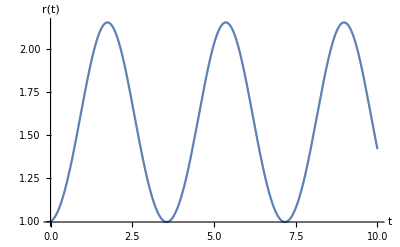

```mathematica
Plot[ Evaluate[ q[[1]] /. solution[t] ] , { t, 0, 10 } , AxesLabel-> { t, q[[1]] }  ]
```

```mathematica
Animate[ 
ParametricPlot[ { solution[t][[1,2]] , solution'[t][[1,2]] } , { t , 0, tmax } , AxesLabel-> { q[[1]] , D[q[[1]], t] } ]  ,
{ tmax , 1 ,25 , 0.5  } ]
```

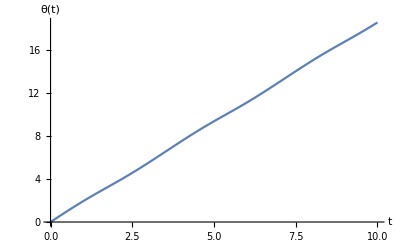

```mathematica
Plot[ Evaluate[ q[[2]] /. solution[t] ]  , { t, 0, 10} ,  AxesLabel-> { t, q[[2]] } ]
```